```mathematica
(*Needs["longskindepthewjn`"]*)
```

```mathematica
(*Table[{x, sphereDipoleField[1, 250, {x, 0, 0}, {0, 0 ,1}]["bZ"][x, 0, 0]}, {x, 2, 10, .5}]*)
```

{{2.,2.61421×10^-8},{2.5,5.61982×10^-9},{3.,1.68509×10^-9},{3.5,6.20129×10^-10},{4.,2.62508×10^-10},{4.5,1.23036×10^-10},{5.,6.22937×10^-11},{5.5,3.34943×10^-11},{6.,1.88895×10^-11},{6.5,1.10682×10^-11},{7.,6.68767×10^-12},{7.5,4.14088×10^-12},{8.,2.61312×10^-12},{8.5,1.67217×10^-12},{9.,1.07963×10^-12},{9.5,6.99515×10^-13},{10.,4.51912×10^-13}}

```mathematica
sphereDipoleFieldPoints = {{2.,2.6142124585971176*^-8},{2.5,5.6198233371519495*^-9},{3.,1.6850866278381694*^-9},{3.5,6.201294361210435*^-10},{4.,2.625078148376947*^-10},{4.5,1.2303620653511336*^-10},{5.,6.229366903553939*^-11},{5.5,3.349431772616367*^-11},{6.,1.8889472855369908*^-11},{6.5,1.106822216445101*^-11},{7.,6.687668797382179*^-12},{7.5,4.140880647713249*^-12},{8.,2.6131198399413383*^-12},{8.5,1.6721669276250677*^-12},{9.,1.0796309812192286*^-12},{9.5,6.995145386687253*^-13},{10.,4.5191194095435516*^-13}};
```

```mathematica
sphereDipoleFieldHigherMeshResolutionPoints = {{6, 2.1718255525669784*^-11}};
```

```mathematica
diffs = MapThread[{#1[[1]], #2[[2]] - #1[[2]]} &, {sphereDipoleFieldPoints, sphereUniformFieldPoints}]
```

{{2.,-9.64532×10^-9},{2.5,-1.29531×10^-9},{3.,-2.36818×10^-10},{3.5,-4.57905×10^-11},{4.,-4.74724×10^-12},{4.5,4.10939×10^-12},{5.,5.27671×10^-12},{5.5,4.6474×10^-12},{6.,3.73971×10^-12},{6.5,2.93075×10^-12},{7.,2.28637×10^-12},{7.5,1.79122×10^-12},{8.,1.41439×10^-12},{8.5,1.12722×10^-12},{9.,9.07019×10^-13},{9.5,7.36751×10^-13},{10.,6.03875×10^-13}}

```mathematica
rsDipoleFieldPoints = {#[[1]] + .25, #[[2]]} & /@ sphereDipoleFieldPoints
```

{{2.25,2.61421×10^-8},{2.75,5.61982×10^-9},{3.25,1.68509×10^-9},{3.75,6.20129×10^-10},{4.25,2.62508×10^-10},{4.75,1.23036×10^-10},{5.25,6.22937×10^-11},{5.75,3.34943×10^-11},{6.25,1.88895×10^-11},{6.75,1.10682×10^-11},{7.25,6.68767×10^-12},{7.75,4.14088×10^-12},{8.25,2.61312×10^-12},{8.75,1.67217×10^-12},{9.25,1.07963×10^-12},{9.75,6.99515×10^-13},{10.25,4.51912×10^-13}}

```mathematica
(*sphereUniformFieldPoints = Table[{x, sphereUniformField[1, 250, 1/(x^3)]["bZ"][x, 0, 0]}, {x, 2, 10, .5}]*)
```

{{2.,-1.64968×10^-8},{2.5,-4.32451×10^-9},{3.,-1.44827×10^-9},{3.5,-5.74339×10^-10},{4.,-2.57761×10^-10},{4.5,-1.27146×10^-10},{5.,-6.75704×10^-11},{5.5,-3.81417×10^-11},{6.,-2.26292×10^-11},{6.5,-1.3999×10^-11},{7.,-8.97404×10^-12},{7.5,-5.9321×10^-12},{8.,-4.02751×10^-12},{8.5,-2.79939×10^-12},{9.,-1.98665×10^-12},{9.5,-1.43627×10^-12},{10.,-1.05579×10^-12}}

```mathematica
sphereUniformFieldPoints = {{2.,1.649680571469782*^-8},{2.5,4.3245129277712425*^-9},{3.,1.4482687339962462*^-9},{3.5,5.743389134522651*^-10},{4.,2.5776057472289147*^-10},{4.5,1.2714559655473036*^-10},{5.,6.75703801414958*^-11},{5.5,3.814171704052086*^-11},{6.,2.26291826063245*^-11},{6.5,1.3998974549172707*^-11},{7.,8.974042451777574*^-12},{7.5,5.932104270870742*^-12},{8.,4.027508188201787*^-12},{8.5,2.7993860729621852*^-12},{9.,1.9866496888852804*^-12},{9.5,1.4362654619010345*^-12},{10.,1.0557870908750322*^-12}}
```

{{2.,1.64968×10^-8},{2.5,4.32451×10^-9},{3.,1.44827×10^-9},{3.5,5.74339×10^-10},{4.,2.57761×10^-10},{4.5,1.27146×10^-10},{5.,6.75704×10^-11},{5.5,3.81417×10^-11},{6.,2.26292×10^-11},{6.5,1.3999×10^-11},{7.,8.97404×10^-12},{7.5,5.9321×10^-12},{8.,4.02751×10^-12},{8.5,2.79939×10^-12},{9.,1.98665×10^-12},{9.5,1.43627×10^-12},{10.,1.05579×10^-12}}

```mathematica
expectedBz[x_]:= 1/(15 x^6 * 250^2)
```

```mathematica
expectedBz[7.0]
```

9.06652×10^-12

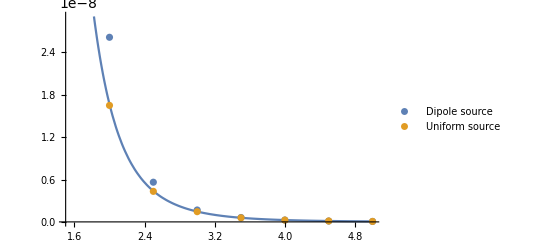

```mathematica
Show[Plot[expectedBz[x], {x, 1.5, 5} (*, PlotLabels -> "Exact uniform field sphere" *)], ListPlot[<|"Dipole source" -> sphereDipoleFieldPoints,"Uniform source" -> sphereUniformFieldPoints |>]]
```

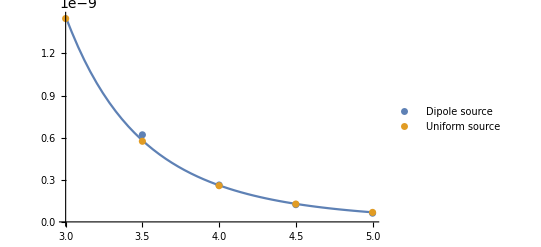

```mathematica
Show[Plot[expectedBz[x], {x, 3, 5} (*, PlotLabels -> "Exact uniform field sphere" *)], ListPlot[<|"Dipole source" -> sphereDipoleFieldPoints,"Uniform source" -> sphereUniformFieldPoints|>]]
```

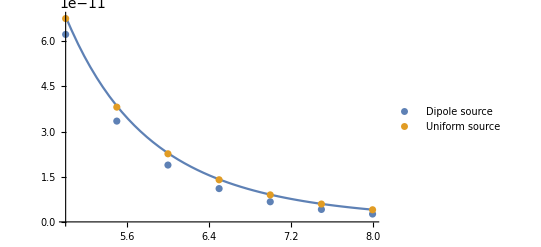

```mathematica
Show[Plot[expectedBz[x], {x, 5, 8} (*, PlotLabels -> "Exact uniform field sphere" *)], ListPlot[<|"Dipole source" -> sphereDipoleFieldPoints,"Uniform source" -> sphereUniformFieldPoints |>]]
```

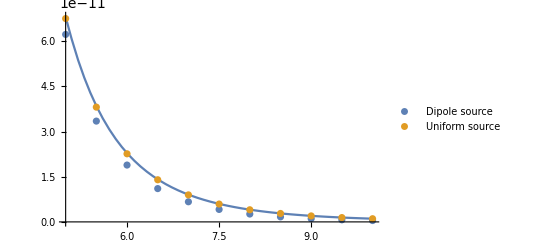

```mathematica
Show[Plot[expectedBz[x], {x, 5, 10} (*, PlotLabels -> "Exact uniform field sphere" *)], ListPlot[<|"Dipole source" -> sphereDipoleFieldPoints,"Uniform source" -> sphereUniformFieldPoints |>]]
```

```mathematica
m = 1.8889472855369908*^-11 * 6^6
```

8.81307×10^-7

```mathematica
f[x_] := (8.813072455401385*^-7) * x^(-6)
```

```mathematica
f[4]
```

2.625×10^-10

```mathematica
f[15]
```

7.73713×10^-14

```mathematica
f[13]
```

1.82586×10^-13

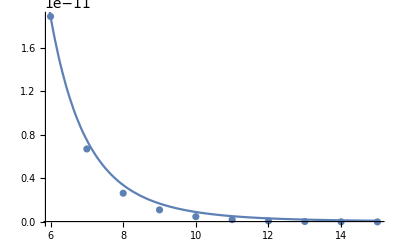

```mathematica
Show[ListPlot[a], Plot[f[x], {x, 5, 15}]]
```